```mathematica
Clear[x,y,z,yexact,youter,yinner,ycomp]
Simplify[DSolve[{ε*y''[x]+(1+ε^2)*y'[x]+(1-ε^2)*y[x]==0,y[0]==0,y[1]==1 },y[x],x]]
```

{{y[x]→(ⅇ^(1+1/ε+ε-x (1+ε)) (-1+ⅇ^(x (2-1/ε+ε))))/(-ⅇ^(1/ε)+ⅇ^(2+ε))}}

We first compute the exact solution with the epsillon included.  The function is smooth, however with a boundary layer at 0.

```mathematica
yexact[x_,ε_]=y[x]/.%
```

{(ⅇ^(1+1/ε+ε-x (1+ε)) (-1+ⅇ^(x (2-1/ε+ε))))/(-ⅇ^(1/ε)+ⅇ^(2+ε))}

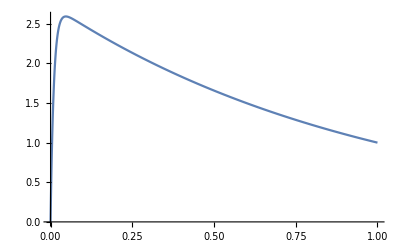

```mathematica
Plot[yexact[x,ε]/.ε->0.01,{x,0,1}]
```

```mathematica
$Outer$
```

$Outer$

```mathematica
DSolve[{y'[x]+y[x]==0,y[1]==1},y[x],x]
```

{{y[x]→ⅇ^(1-x)}}

```mathematica
youter[x_]=y[x]/.%
```

{ⅇ^(1-x)}

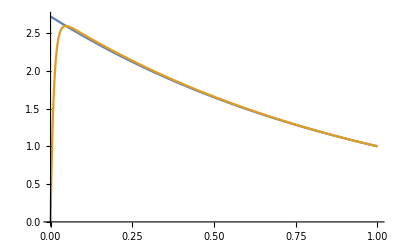

```mathematica
Plot[{youter[x],yexact[x,ε]/.ε->0.01},{x,0,1}]
```

```mathematica
$Inner$
```

$Inner$

As we already mentioned above, as the boundary layer is at x=0, one needs to study the inner solution on the problematic domain. Then using Van Dyke Matching or composite we can join both solutions and compare it with the exact solution.

```mathematica
Simplify[DSolve[{y''[x]+y'[x]==0,y[0]==0},y[x],x]]
yinner[x_]=y[x]/.%
```

{{y[x]→(1-ⅇ^-x) C[1]}}

{(1-ⅇ^-x) C[1]}

```mathematica
y
```

```mathematica
Limit[yinner[x],x->∞]-Limit[youter[x],x->0]
Solve[%==0,C[1]]
```

{-ⅇ+C[1]}

{{C[1]→ⅇ}}

```mathematica
h=C[1]/.%
```

{ⅇ}

```mathematica
ycomp[x_,ε_]=youter[x]+yinner[x/ε]-Exp[1]
```

{-ⅇ+ⅇ^(1-x)+(1-ⅇ^(-x/ε)) C[1]}

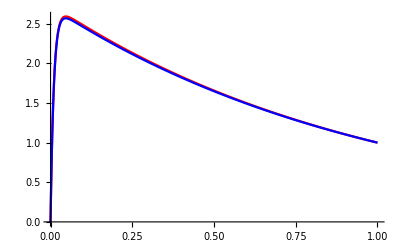

```mathematica
Plot[{yexact[x,0.01],ycomp[x,0.01]/.C[1]-> h},{x,0,1},PlotStyle->{Red,Blue}]
```